```mathematica
data = Import["~/Desktop/moodys/distance-time-pairs-2.csv"]
```

{{0.619751,34.0863},{0.656979,36.1338},{0.656979,36.1338},{0.842472,46.3359},{0.908489,49.9669},{0.908489,49.9669},{0.611012,33.6056},{0.491308,27.022},{0.491308,27.022},{0.491308,27.022},{0.605247,33.2886},20190,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}
 |  |  |  |

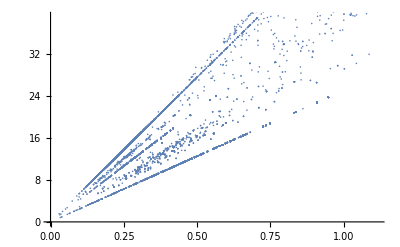

```mathematica
ListPlot[data]
```

```mathematica
Show[%20,ImageSize->Full]
```

-Graphics-

```mathematica
Show[%21,AxesLabel->{HoldForm[Time in hours],HoldForm[Distance in miles]},PlotLabel->HoldForm[U.S.(Commuter:Distance and Time Variability)],LabelStyle->{16,GrayLevel[0]}]
```

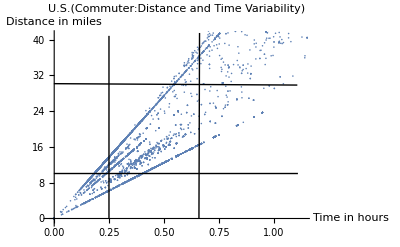

```mathematica
SplitBy[data]
```

{{{0.619751,34.0863}},3795,{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},10332,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}
 |  |  |  |